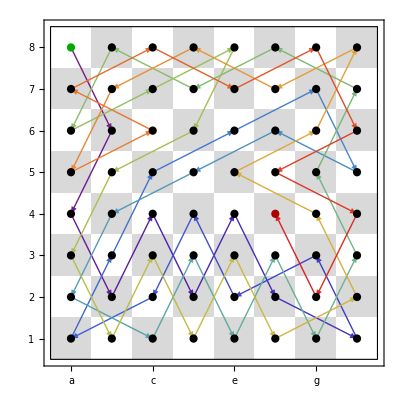

```mathematica
(*1. List of indices (top left=1;numbering row-by-row to 64)*)

indices = {1,18,33,50,35,52,37,54,64,47,53,36,51,57,42,27,21,15,32,22,28,34,49,59,44,61,46,63,48,31,16,6,12,2,17,11,5,20,26,41,58,43,60,45,62,56,39,29,23,8,14,4,10,25,19,9,3,13,7,24,30,40,55,38};


(*2. Convert an index to the center coordinate of the corresponding chess square.-Use 0-based column:col=Mod[index-1,8]-Use 0-based row (with row 0=top row,row 7=bottom):row=Quotient[index-1,8] The center of a square is at {col+0.5,(7-row)+0.5}.For example,index 1 becomes {0.5,7.5} (a8),and index 64 becomes {7.5,0.5} (h1).*)
centeredCoords=Table[{Mod[idx-1,8]+0.5,7-Quotient[idx-1,8]+0.5},{idx,indices}];

(*3. Build the chessboard background.We let:-c run from 0 to 7 for columns (file a=0,h=7)-r run from 0 to 7 for rows (r=0 represents rank 8,r=7 represents rank 1).To ensure h1 (file h,rank 1:c=7,r=7) is white,we set the coloring so that:if EvenQ[c+r] then White,else LightGray.For example:a8:{c=0,r=0}->0+0=0 (even)->White;
h8:{c=7,r=0}->7 (odd)->LightGray;
a1:{c=0,r=7}->7 (odd)->LightGray;
h1:{c=7,r=7}->14 (even)->White.*)
chessboard=Flatten[Table[{If[EvenQ[c+r],White,LightGray],Rectangle[{c,7-r},{c+1,8-r}]},{r,0,7},{c,0,7}],1];

(*Add a thick black border around the board.*)
boardBorder={FaceForm[None],EdgeForm[{Black,Thick}],Rectangle[{0,0},{8,8}]};

(*4. Create rainbow-colored arrows connecting consecutive centered coordinates.We use ColorData["Rainbow"] to create a gradient.*)
arrowCount=Length[centeredCoords]-1;
rainbowArrows=Table[{ColorData["Rainbow"][(i-1)/(arrowCount-1)],Arrow[{centeredCoords[[i]],centeredCoords[[i+1]]}]},{i,1,arrowCount}];

(*5. Define frame ticks:-x-axis (files):centers at 0.5,1.5,…,7.5 with labels "a" through "h"-y-axis (ranks):centers at 0.5,1.5,…,7.5 with labels "1" through "8"*)
xTicks=Table[{i+0.5,CharacterRange["a","h"][[i+1]]},{i,0,7}];
yTicks=Table[{i+0.5,i+1},{i,0,7}];

(*6. Draw disks with a smaller radius.Only the first disk (first index) is red;the remaining disks are black.*)
diskRadius=0.1;
circles=Join[{Style[Disk[centeredCoords[[1]],diskRadius],Darker[ Green]]},Table[Style[Disk[centeredCoords[[i]],diskRadius],Black],{i,2,Length[centeredCoords]-1}],{Style[Disk[centeredCoords[[-1]],diskRadius],Darker[ Red]]}];


(*7. Combine everything into one graphic.*)
Graphics[{chessboard,boardBorder,rainbowArrows,circles},AspectRatio->1,Frame->True,FrameTicks->{xTicks,yTicks,xTicks,yTicks},ImageSize->400]
```